```mathematica
(*Importamos archivos de EoS*)
ClearAll["Global`*"];
SoftRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Soft.txt", "Table"][[All,1]]; SoftP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Soft.txt", "Table"][[All,2]];
Soft = Transpose[{Flatten[SoftP], Flatten[SoftRho]}];
MidRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Mid.txt", "Table"][[All,1]]; MidP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Mid.txt", "Table"][[All,2]];
Mid = Transpose[{Flatten[MidP], Flatten[MidRho]}];
StiffRho = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Stiff.txt", "Table"][[All,1]]; StiffP = Import["/Users/neturo/Desktop/Máster/TFM/Resultados/Datos/EoS/Stiff.txt", "Table"][[All,2]];
Stiff = Transpose[{Flatten[StiffP], Flatten[StiffRho]}];
```

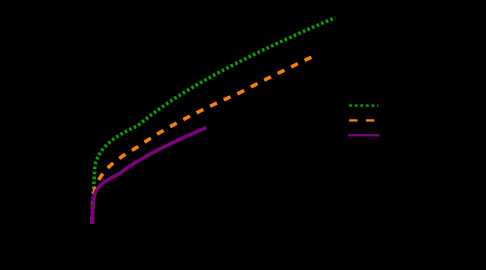

```mathematica
(*Definimos las ecuaciones de estado*)
ρSoft=Quiet[Interpolation[Soft,InterpolationOrder->1]];
ρMid=Quiet[Interpolation[Mid,InterpolationOrder->1]];
ρStiff=Quiet[Interpolation[Stiff,InterpolationOrder->1]];

(* Creamos los plots de cada una *)
SoftPlot=Plot[ρSoft[P],{P,Min[SoftP],Max[SoftP]},PlotStyle->{Darker[Green],Thickness[0.007],Dashing[0.005]}];

MidPlot=Plot[ρMid[P],{P,Min[MidP],Max[MidP]},PlotStyle->{Orange,Thickness[0.007],Dashing[0.015]}];

StiffPlot=Plot[ρStiff[P],{P,Min[StiffP],Max[StiffP]},PlotStyle->{Purple,Thickness[0.007]}];

(* Mostramos los plots con su leyenda *)
Legended[Show[SoftPlot,MidPlot,StiffPlot,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[FontSize->10,Black],FrameLabel->{"P / km^-2","ρ / km^-2"},AspectRatio->3/4,ImageSize->Medium,Background->Transparent,BaseStyle->{FontFamily->"Helvetica",FontSize->12},PlotRange->All],Placed[LineLegend[{{Darker[Green],Thickness[0.007],Dashing[0.005]},{Orange,Thickness[0.007],Dashing[0.015]},Purple},{Style["Soft",10],Style["Middle",10],Style["Stiff",10]},LegendFunction->(Framed[#,FrameStyle->Black,Background->White,FrameMargins->0]&),LegendMarkerSize->{30,2},LabelStyle->(FontFamily->"Helvetica"),Spacings->0.15],{0.17,0.81}]]
```

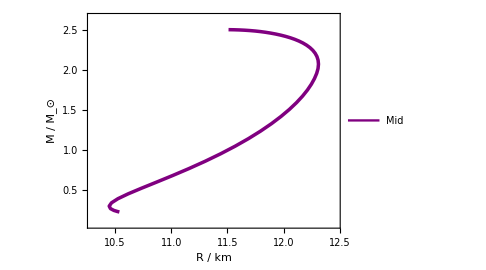

```mathematica
(* Constantes y valores iniciales *)
Msol=1.4763 (*Factor en unidades naturales*);
rinit=10^-10 (*km*);
Ainit=0.1;
G=1;
c=1;

(* Aquí decidimos qué EoS usar *)
ρ=ρMid;


(* Definimos el número de valores de Pinit y el rango, que depende de la EoS*)
numValues=50;
PinitMin=6.*10^-6;
PinitMax=Max[MidP];

(* Generamos una lista de valores de Pinit espaciados con un factor ξ *)
ξ=2.5;
PinitValues=Table[PinitMin+(PinitMax-PinitMin)*(i^ξ-1)/(numValues^ξ-1),{i,numValues}];

PRM={};

(* Iteramos sobre cada valor de Pinit, pero antes decidimos si mostrar distribuciones para cada presión o no *)
MostrarGraficas=False;
Do[
(* Resolvemos el sistema de ecuaciones *)
EoS={ρ[P]};
de1=P'[r]==-G*ρ[P[r]]*m[r] (1+P[r]/(ρ[P[r]]*c^2)) r^-2 (1+4 Pi*r^3 P[r]/(m[r]*c^2)) (1-2 G*m[r]/(r*c^2))^-1;
de2=m'[r]==4 Pi r^2 ρ[P[r]];
de3= (A'[r])/A[r]==(2*G*(m[r]+4*π*r^3*P[r]))/(r*(r-2*G*m[r]));
de={de1,de2,de3};
init={P[rinit]==Pinit,m[rinit]==10^-50,A[rinit]==Ainit,WhenEvent[m'[r]<=10^-20,{rtot=r, mtot=m[r], "StopIntegration"}]};
rtot=500;

(* AQUÍ ESTÁ EL NDSOLVE *)
sol=Quiet[NDSolve[{de,init},{P[r],m[r],A[r]},{r,rinit,500},WorkingPrecision->35],{NDSolve::precw,InterpolatingFunction::dmval}];

guardar={Pinit,rtot,mtot/Msol};
AppendTo[PRM,guardar];

(* Extraemos las soluciones *)
pder=sol[[1]][[1]]/. Rule->(#2&);
mder=sol[[1]][[2]]/. Rule->(#2&);
mder=mder/Msol;
Ader=sol[[1]][[3]]/. Rule->(#2&);
(* Calculamos también B(r) a partir de m(r) *)
B=(1-(2*G*mder)/r)^(-1);


(* Calculamos la derivada numérica de P(r) *)
pderivative=D[pder,r];

(* Aquí empiezan las representaciones para cada presión central *)
If[MostrarGraficas,
(* Valores del radio y la masa total de la estrella *)
Print[StringForm["Pinit = ``",DecimalForm[Pinit,ScientificNotationThreshold->{1,1}]]];
Print[StringForm["Radio de la estrella: `` km",NumberForm[rtot]]];
Print[StringForm["Masa total de la estrella: `` ``",NumberForm[mtot/Msol],ToString[Subscript["M","⊙"],StandardForm]]];

(* Representamos P(r) *)
plotP=Plot[pder,{r,rinit,rtot},PlotStyle->{Purple,Thickness[0.01]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","P(r)"},PlotLabel->StringForm["Perfil de presión para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"P(r)"},ImageSize->Medium];

(* Representamos m(r) *)
plotm=Plot[mder,{r,rinit,rtot},PlotStyle->{Purple,Thickness[0.01]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","m(r)"},PlotLabel->StringForm["Perfil de masa para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"m(r)"},ImageSize->Medium];

(* Hacemos display de estos dos plots *)
Print[plotP,plotm];

(* Representamos A(r) *)
plotA= Plot[Ader,{r,rinit,rtot},PlotStyle->{Orange,Thickness[0.007]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","A(r)"},PlotLabel->StringForm["Coeficiente A en el interior para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"A(r)"},ImageSize->Medium];

(* Representamos B(r) *)
plotB=Plot[B,{r,rinit,rtot},PlotStyle->{Orange,Thickness[0.007]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","B(r)"},PlotLabel->StringForm["Coeficiente B en el interior para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"B(r)"},ImageSize->Medium];

(* Hacemos display de estos dos plots *)
Print[plotA,plotB];

(* Representamos P'(r) *)
Print[Plot[pderivative,{r,rinit,rtot},PlotStyle->{Darker[Green],Thickness[0.005]},Ticks->{ScientificForm},Frame->True,FrameLabel->{"r","P'(r)"},PlotLabel->StringForm["Derivada de la presión de la estrella para Pinit = ``",NumberForm[Pinit,ScientificNotationThreshold->{2,2}]],AspectRatio->3/4,PlotLegends -> {"P'(r)"}]];

(* Comprobaciones de validez de la presión central *)
If[MaxValue[{pderivative,rinit<r<rtot},r]>=0,Print[Style["El perfil de presión no es estrictamente decreciente.",Red]],Print[Style["El perfil de presión es estrictamente decreciente.",Darker[Green]]]];
If[MinValue[{pder,rinit<r<rtot},r]>MaxValue[{pder,rinit<r<rtot},r]/100,Print[Style["El perfil de presión no alcanza el 0.",Red]],Print[Style["El perfil de presión alcanza el 0.",Darker[Green]]]];
Print["\n---------------------------------------------------------------------------------------------------------\n---------------------------------------------------------------------------------------------------------\n---------------------------------------------------------------------------------------------------------\n"]
];

Clear[rtot,mtot],
{Pinit,PinitValues}]

(* Extraemos valores de radio y masa para hacer el diagrama *)
RM=PRM[[All,{2,3}]];

(* Damos márgenes fijos para la visualización y representamos *)
margin=0.15;
ListLinePlot[RM,PlotStyle->{Purple,Thickness[0.007]},PlotRange->{{Min[RM[[All,1]]]-margin,Max[RM[[All,1]]]+margin},{Min[RM[[All,2]]]-margin,Max[RM[[All,2]]]+margin}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[FontSize->10,Black],FrameLabel->{"R / km","M / M_⊙"},AspectRatio->3/4,PlotLegends->Placed[LineLegend[{Style["Mid",12]},LegendFunction->(Framed[#,FrameStyle->Black,Background->White,FrameMargins->Tiny]&),LegendMarkerSize->{30,2}],{0.17,0.75}],ImageSize->Medium,BaseStyle->{FontFamily->"Helvetica",FontSize->12}]
```

```mathematica
Export["/Users/neturo/Desktop/StiffMR.txt",RM,"Table"]
```

/Users/neturo/Desktop/StiffMR.txt